# FlightsOverhead

Determine the flights and flight paths of airplanes currently overhead at a location

## Definition

```mathematica
(*messages*)FlightsOverhead::notloc="`1` is not a valid location.";
FlightsOverhead::notair="`1` is not an airline entity.";

(*UI*)
FlightsOverhead[args___]:=With[{res=iFlightsOverhead[args]},res/;res=!=$Failed]

(*main code*)
iFlightsOverhead[]:=iFlightsOverhead[Here,"PropertyAssociation",All]
iFlightsOverhead["Properties"]:={"Flights","SkyMap"}
iFlightsOverhead[loc_]:=iFlightsOverhead[loc,"PropertyAssociation",All]
iFlightsOverhead[loc_,prop_]:=iFlightsOverhead[loc,prop,All]
iFlightsOverhead[loc_,prop_,airline_]:=Module[{pos,data,a=airline/.Entity["Airline",x_]:>x,p},pos=formatposition[loc];
If[pos===$Failed,ResourceFunction["ResourceFunctionMessage"][FlightsOverhead::notloc,loc];Return[$Failed]];
If[!(StringQ[a]||a===All),ResourceFunction["ResourceFunctionMessage"][FlightsOverhead::notair,airline];Return[$Failed]];
If[MemberQ[{"Flights","PropertyAssociation","SkyMap"},prop],p=prop/.{("SkyMap"|"PropertyAssociation")->{"FlightId","Longitude","Latitude","Altitude"}},ResourceFunction["ResourceFunctionMessage"][General::notprop,prop,FlightsOverhead];
Return[$Failed]];
data=iFlightOverheadBatchQuery[pos,p,a];
If[prop==="PropertyAssociation",Association[#->formatprop[data,#,pos]&/@{"Flights","SkyMap"}],formatprop[data,prop,pos]]]
iFlightsOverhead[args___]:=(ResourceFunction["ResourceFunctionMessage"][General::argb,FlightsOverhead,Length[{args}],0,3];$Failed)

formatposition[{lat_,long_,___}]:=GeoPosition[{lat,long}/.Quantity[a_,"AngularDegrees"]:>a]
formatposition[GeoPosition[coord:{_,_,___},___]]:=GeoPosition[coord/.Quantity[a_,"AngularDegrees"]:>a]
formatposition[e_Entity]:=Module[{pos=Quiet[EntityValue[e,"Position"],{Entity::etype,EntityProperty::qname,EntityProperty::pname,EntityValue::pname}]},formatposition[pos]]
formatposition[__]:=$Failed
```

```mathematica
$batchnumber=10;
iFlightOverheadBatchQuery[e_,prop_,airline_]:=Module[{p=prop,entities,input,data,dates=DateList[Now,TimeZone->"UTC"]},input=Internal`MWASymbols`MWAFlightData[e,{"StandardName"},airline,All];
entities=Flatten[flightAPI[input]];
If[MatchQ[entities,{}|_Missing],Return[Missing["NotAvailable"]]];
dates={DatePlus[dates,Quantity[-2,"Hours"]],dates};
If[prop==="Flights",Return[entities]];
entities=Partition[entities,$batchnumber,$batchnumber,{1,1},Nothing];
DynamicModule[{progress=0,text},If[TrueQ[$Notebooks],text=Row[{"Downloading ",Dynamic[progress]," of ",ToString[Length[Flatten[entities]]]," flights...."}];
PrintTemporary[Internal`LoadingPanel[text]]];
data=Flatten[Table[progress=progress+Length[x];
input=Internal`MWASymbols`MWAFlightData[x,p,airline,dates];
input=flightAPI[input];
Which[MatchQ[input,_Missing],Table[Table[Missing["NotAvailable"],{j,Length[p]}],{i,Length[x]}],Length[x]===1,{input},True,input],{x,entities}],1];
progress=Length[Flatten[entities]];];
(*sift out unneeded entities due to specific airline*)If[FreeQ[data,None],Which[Length[Flatten[entities]]===1&&Length[p]<2,{Flatten[entities],{data}},True,{Flatten[entities],data}],DeleteCases[Transpose[{Flatten[entities],data}],_?(!FreeQ[#,None]&)]]]
```

```mathematica
flightAPI[input_]:=Module[{result,messages},result=Internal`MWACompute["MWAFlightData",input,"ContextPath"->{"Internal`MWASymbols`","System`","DataPaclets`FlightDataDump`"},"MessageHead"->FlightData];
If[FreeQ[result,$Failed],result=ReleaseHold[result];messages="Messages"/.result,If[Not[FreeQ[result,"ComputationTimeout"]],ResourceFunction["ResourceFunctionMessage"][FlightsOverhead::timeout,FlightsOverhead]];
result=$Failed];
messages=Cases[messages,Hold[Message[MessageName[FlightData,_],___]]];
ReleaseHold[messages];
If[FreeQ[result,"Result"],result/.$Failed->Missing["NotAvailable"],"Result"/.result/.$Failed->Missing["NotAvailable"]]]

formatprop[_Missing,_,_]:=Missing["NotAvailable"]
formatprop[f:{_Integer..},"Flights",_]:=Entity["Flight",ToString[#]]&/@f
formatprop[{f:{_Integer..},__},"Flights",_]:=Entity["Flight",ToString[#]]&/@f
formatprop[data_,"SkyMap",pov_]:=Module[{idate=data[[2,All,2,1,1]]},idate=Last[SortBy[idate,AbsoluteTime]];
iFlightSkyMap[data,idate,pov]]

formatprop[__]:=Missing["NotAvailable"]
```

```mathematica
iFlightSkyMap[data_,idate_,pov_GeoPosition]:=Module[{cleandata=data[[2,All,2;;]],id,arrow},id=Entity["Flight",ToString[#]]&/@data[[1]];
cleandata=Map[{#[[1]],#[[2]],With[{avgAlt=Replace[Mean@Cases[#[[3]][[All,-1]],_?NumericQ],Except[_?NumericQ]->10000]},Replace[#[[3]],{t_,alt_Missing}:>{t,avgAlt},{1}]]}&,cleandata];
cleandata[[All,3,All,2]]*=(381/1250);
cleandata=Map[If[MatchQ[#,{__List}],Transpose[{#[[1,All,1]],Transpose[#[[All,All,2]]]}],#]&,cleandata];
With[{pos=Position[!MemberQ[#,_Missing,Infinity,Heads->True]&/@cleandata,True]},cleandata=Extract[cleandata,pos]];
cleandata[[All,All,1]]=(Round[AbsoluteTime[idate]]-Map[Round[AbsoluteTime[#]]&,cleandata[[All,All,1]],{2}]);
cleandata=Cases[cleandata,{{_?NumericQ,{__?NumericQ}}..}];
If[cleandata==={},Return[Missing["NotAvailable"]]];
cleandata=Quiet[Interpolation[#,InterpolationOrder->1],{InterpolatingFunction::dmval}]&/@cleandata;
Quiet[With[{ptrange=Range[0,500,25],blend=Table[Blend[{{0,GrayLevel[0.7]},{1,GrayLevel[1]}},i],{i,Range[0,500,25]/500}]},arrow=MapThread[Function[{if,name},With[{pts=if/@ptrange},{Opacity[.5],Thick,{Opacity[1],Thread[{Most[blend],Line/@Partition[pts,2,1]}]},Opacity[0],Tooltip[Arrow[pts[[{2,1}]]],name]}]],{cleandata,id}]],{InterpolatingFunction::dmval}];
(*evaluate the star chart code*)SkyChart[{PointSize[Large],FlightDataAirplane[1,Red,1,True],arrow},pov,DateObject[TimeZone->"GMT"]]]
```

```mathematica
FlightDataAirplane[pos_,color_:Red,opacity_:1,offsetq_:False]:=Arrowheads[{{.05,Clip[pos,{0,1}],Graphics[{Opacity[opacity],Text[Style[FromCharacterCode[40,"ZapfDingbats"],FontSize->Round[1.6 14],FontColor->color,If[$OperatingSystem==="Windows",FontFamily->"MS Mincho",Sequence@@{}]]]}]}}]
```

```mathematica
deltaT0modern=Interpolation[N@{(*Data from 1620 to 2009 taken from https://webspace.science.uu.nl/~gent0113/deltat/deltat_modern.htm*){1620,124},{1621,119},{1622,115},{1623,110},{1624,106},{1625,102},{1626,98},{1627,95},{1628,91},{1629,88},{1630,85},{1631,82},{1632,79},{1633,77},{1634,74},{1635,72},{1636,70},{1637,67},{1638,65},{1639,63},{1640,62},{1641,60},{1642,58},{1643,57},{1644,55},{1645,54},{1646,53},{1647,51},{1648,50},{1649,49},{1650,48},{1651,47},{1652,46},{1653,45},{1654,44},{1655,43},{1656,42},{1657,41},{1658,40},{1659,38},{1660,37},{1661,36},{1662,35},{1663,34},{1664,33},{1665,32},{1666,31},{1667,30},{1668,28},{1669,27},{1670,26},{1671,25},{1672,24},{1673,23},{1674,22},{1675,21},{1676,20},{1677,19},{1678,18},{1679,17},{1680,16},{1681,15},{1682,14},{1683,14},{1684,13},{1685,12},{1686,12},{1687,11},{1688,11},{1689,10},{1690,10},{1691,10},{1692,9},{1693,9},{1694,9},{1695,9},{1696,9},{1697,9},{1698,9},{1699,9},{1700,9},{1701,9},{1702,9},{1703,9},{1704,9},{1705,9},{1706,9},{1707,9},{1708,10},{1709,10},{1710,10},{1711,10},{1712,10},{1713,10},{1714,10},{1715,10},{1716,10},{1717,11},{1718,11},{1719,11},{1720,11},{1721,11},{1722,11},{1723,11},{1724,11},{1725,11},{1726,11},{1727,11},{1728,11},{1729,11},{1730,11},{1731,11},{1732,11},{1733,11},{1734,12},{1735,12},{1736,12},{1737,12},{1738,12},{1739,12},{1740,12},{1741,12},{1742,12},{1743,12},{1744,13},{1745,13},{1746,13},{1747,13},{1748,13},{1749,13},{1750,13},{1751,14},{1752,14},{1753,14},{1754,14},{1755,14},{1756,14},{1757,14},{1758,15},{1759,15},{1760,15},{1761,15},{1762,15},{1763,15},{1764,15},{1765,16},{1766,16},{1767,16},{1768,16},{1769,16},{1770,16},{1771,16},{1772,16},{1773,16},{1774,16},{1775,17},{1776,17},{1777,17},{1778,17},{1779,17},{1780,17},{1781,17},{1782,17},{1783,17},{1784,17},{1785,17},{1786,17},{1787,17},{1788,17},{1789,17},{1790,17},{1791,17},{1792,16},{1793,16},{1794,16},{1795,16},{1796,15},{1797,15},{1798,14},{1799,14},{1800,13.7},{1801,13.4},{1802,13.1},{1803,12.9},{1804,12.7},{1805,12.6},{1806,12.5},{1807,12.5},{1808,12.5},{1809,12.5},{1810,12.5},{1811,12.5},{1812,12.5},{1813,12.5},{1814,12.5},{1815,12.5},{1816,12.5},{1817,12.4},{1818,12.3},{1819,12.2},{1820,12.0},{1821,11.7},{1822,11.4},{1823,11.1},{1824,10.6},{1825,10.2},{1826,9.6},{1827,9.1},{1828,8.6},{1829,8.0},{1830,7.5},{1831,7.0},{1832,6.6},{1833,6.3},{1834,6.0},{1835,5.8},{1836,5.7},{1837,5.6},{1838,5.6},{1839,5.6},{1840,5.7},{1841,5.8},{1842,5.9},{1843,6.1},{1844,6.2},{1845,6.3},{1846,6.5},{1847,6.6},{1848,6.8},{1849,6.9},{1850,7.1},{1851,7.2},{1852,7.3},{1853,7.4},{1854,7.5},{1855,7.6},{1856,7.7},{1857,7.7},{1858,7.8},{1859,7.8},{1860,7.88},{1861,7.82},{1862,7.54},{1863,6.97},{1864,6.40},{1865,6.02},{1866,5.41},{1867,4.10},{1868,2.92},{1869,1.82},{1870,1.61},{1871,0.10},{1872,-1.02},{1873,-1.28},{1874,-2.69},{1875,-3.24},{1876,-3.64},{1877,-4.54},{1878,-4.71},{1879,-5.11},{1880,-5.40},{1881,-5.42},{1882,-5.20},{1883,-5.46},{1884,-5.46},{1885,-5.79},{1886,-5.63},{1887,-5.64},{1888,-5.80},{1889,-5.66},{1890,-5.87},{1891,-6.01},{1892,-6.19},{1893,-6.64},{1894,-6.44},{1895,-6.47},{1896,-6.09},{1897,-5.76},{1898,-4.66},{1899,-3.74},{1900,-2.72},{1901,-1.54},{1902,-0.02},{1903,1.24},{1904,2.64},{1905,3.86},{1906,5.37},{1907,6.14},{1908,7.75},{1909,9.13},{1910,10.46},{1911,11.53},{1912,13.36},{1913,14.65},{1914,16.01},{1915,17.20},{1916,18.24},{1917,19.06},{1918,20.25},{1919,20.95},{1920,21.16},{1921,22.25},{1922,22.41},{1923,23.03},{1924,23.49},{1925,23.62},{1926,23.86},{1927,24.49},{1928,24.34},{1929,24.08},{1930,24.02},{1931,24.00},{1932,23.87},{1933,23.95},{1934,23.86},{1935,23.93},{1936,23.73},{1937,23.92},{1938,23.96},{1939,24.02},{1940,24.33},{1941,24.83},{1942,25.30},{1943,25.70},{1944,26.24},{1945,26.77},{1946,27.28},{1947,27.78},{1948,28.25},{1949,28.71},{1950,29.15},{1951,29.57},{1952,29.97},{1953,30.36},{1954,30.72},{1955,31.07},{1956,31.35},{1957,31.68},{1958,32.18},{1959,32.68},{1960,33.15},{1961,33.59},{1962,34.00},{1963,34.47},{1964,35.03},{1965,35.73},{1966,36.54},{1967,37.43},{1968,38.29},{1969,39.20},{1970,40.18},{1971,41.17},{1972,42.23},{1973,43.37},{1974,44.49},{1975,45.48},{1976,46.46},{1977,47.52},{1978,48.53},{1979,49.59},{1980,50.54},{1981,51.38},{1982,52.17},{1983,52.96},{1984,53.79},{1985,54.34},{1986,54.87},{1987,55.32},{1988,55.82},{1989,56.30},{1990,56.86},{1991,57.57},{1992,58.31},{1993,59.12},{1994,59.99},{1995,60.78},{1996,61.63},{1997,62.30},{1998,62.97},{1999,63.47},{2000,63.83},{2001,64.09},{2002,64.30},{2003,64.47},{2004,64.57},{2005,64.69},{2006,64.85},{2007,65.15},{2008,65.46},{2009,65.78},(*Data from 2010 to 2019 taken from http://astro.ukho.gov.uk/nao/lvm/*){2010,66.06},{2011,66.33},{2012,66.60},{2013,66.92},{2014,67.30},{2015,67.69},{2016,68.04},{2017,68.60},{2018,68.97},{2019,69.20},(*Value from https://en.wikipedia.org/wiki/DeltaT for January 2020*){2020,69.361}}];

(*restricted to current date which allows us to shrink this*)
deltaT1[year_]:=If[1620≤year≤2020,deltaT0modern[year]/86400,(*This is (-20+32 t^2)/86400,with t=(year-1820)/100,to compare with the deltat NASA webpage above.There is a large discontinuity of about 32 seconds in the transition from deltaT0 to this formula around 2020.*)2449/20000-(91 year)/675000+year^2/27000000]
```

```mathematica
JDToMeanSiderealRadians[jd_]:=With[{T=(jd-2451545.0)/36525},-1.5445680047164863*^7+6.300388098984957 (jd-deltaT1[2000+100 T])+6.770708127139162*^-6 T^2-4.508729661571505*^-10 T^3]
```

```mathematica
JDToMeanSiderealRadians[list_List]:=JDToMeanSiderealRadians/@list;
```

```mathematica
SkyChart1[{x_,y_}]:=(2 y/Pi-1) {-Sin[x],Cos[x]}
```

```mathematica
SkyChart0[Point[x_]]:=Point[SkyChart1[x]]

SkyChart0[Line[{x___List},args___]]:=Line[SkyChart1/@{x},args]

SkyChart0[Arrow[{x___List},args___]]:=Arrow[Prepend[#[[All,2]],#[[1,1]]],args]&/@Split[Partition[SkyChart1/@{x},2,1],#[[2]]==#2[[1]]&]

SkyChart0[Polygon[{x___List}]]:=Polygon/@Select[Split[SkyChart1/@{x},Min[Norm/@{##}]<1.5&],Min[Norm/@#1]<1.2&]

SkyChart0[Circle[{x_,y_},r__]]:=Circle[SkyChart1[{x,y}],r]

SkyChart0[Disk[{x_,y_},r__]]:=Disk[SkyChart1[{x,y}],r]

SkyChart0[Text[a_,{x_,y_},b___]]:=Text[a,SkyChart1[{x,y}],b]

SkyChart0[Rotate[a_,b_,{x_,y_}]]:=Rotate[a,b+x,SkyChart1[{x,y}]]

SkyChart0[x_]:=x;
```

```mathematica
circleIntercept[p1_,p2_]:=Module[{soln=Solve[#.#&[t (p2-p1)+p1]==1&&0≤t≤1,t]},If[MatchQ[soln,{{_Rule}}],p1+(p2-p1) (t/.First@soln),{}]]
```

```mathematica
cropPrimitive[Line[a_]]:=Module[{signs=Sign[Total[a^2,{2}]-1],r},If[Max@signs≤0,Line[a],r=Replace[Partition[Thread[{a,signs}],2,1],{{{p1_,1},{p2_,-1}}:>{{circleIntercept[p1,p2],0},{p2,-1}},{{p1_,-1},{p2_,1}}:>{{p1,-1},{circleIntercept[p1,p2],0}}},{1}];
ReplaceList[r,{{q:({{_,-1},{_,-1}}...),{{p1_,-1},{p2_,0}},___}:>Line@Join[{q}[[All,1,1]],{p1,p2}],{___,{{p1_,0},{_,-1}},Shortest[q___],{{p2_,-1},{p3_,0}},___}:>Line@Join[{p1},{q}[[All,1,1]],{p2,p3}],{___,{{p1_,0},{p2_,-1}},q:({{_,-1},{_,-1}}...)}:>Line@Join[{p1,p2},{q}[[All,2,1]]]}]]]

cropPrimitive[Polygon[a_]]:=Module[{signs=Sign[Total[a^2,{2}]-1],r},r=Thread[{Range@Length@a,a,signs}];
If[Max@signs≤0,Polygon[a],Replace[Partition[r,2,1,1],{{{i_,p1_,1},{_,p2_,-1}}:>(r[[i,{2,3}]]={circleIntercept[p1,p2],0}),{{_,p1_,-1},{i_,p2_,1}}:>(r[[i,{2,3}]]={circleIntercept[p1,p2],0})},{1}];
Polygon[Pick[r[[All,2]],r[[All,3]],0|-1]]]]

cropPrimitive[Disk[a_,r_?NumericQ]]:=Module[{d=Sqrt[a.a],s,t,q,c=ArcTan@@a},Which[r+d<1,Disk[a,r],r+1<d,{},r<d+1,s=Solve[Thread[{Cos[t],Sin[t]}==a+r {Cos[q],Sin[q]}],{t,q},InverseFunctions->True];
{DiskSegment[a,r,Sort@Mod[q/.s,2 Pi,c]],EdgeForm[None],DiskSegment[{0,0},1,Sort@Mod[t/.s,2 Pi,c-Pi]]},True,{}]]

cropPrimitive[Circle[{0,0},r__]]:=Circle[{0,0},r]

cropPrimitive[Circle[a_,r_]]:=Module[{d=Sqrt[a.a],s,t,q,c=ArcTan@@a},If[Abs[d-1]≤r<d+1,s=Solve[Thread[{Cos[t],Sin[t]}==a+r {Cos[q],Sin[q]}],{t,q},InverseFunctions->True];
Circle[a,r,Sort@Mod[q/.s,2 Pi,c]],Circle[a,r]]]

cropPrimitive[Rotate[g_,a_,o_]]:=Module[{d},d=g/.Disk[c_,r_,q_:{0,2 Pi}]:>Polygon@Table[c+r {Cos[t],Sin[t]},{t,Subdivide[q[[1]],q[[2]],20]}];
d/.Polygon[pts_]:>cropPrimitive@Polygon@RotationTransform[a,o][pts]]

cropPrimitive[other_]:=other
```

```mathematica
cropGraphic[g_]:=g/.l_Line|l_Polygon|l_Circle|l_Disk|l_Rotate:>cropPrimitive[l]

iSkyChart[primitives_,opts:OptionsPattern[]]:=Labeled[cropGraphic@Graphics[MapAll[SkyChart0,primitives],Background->None,PlotRange->{{-1,1},{-1,1}},PlotRangePadding->.03],Text[Style[#]]&/@Replace[{"N","W","S","E"},{{n_,w_,s_,e_}:>{s,e,n,w},_->{"","","",""}}],All,FrameMargins->5]
```

```mathematica
LocalHorizon[h_,dec_,lat_]:={ArcTan[Cos[h] Sin[lat]-Tan[dec] Cos[lat],Sin[h]],ArcSin[Sin[lat] Sin[dec]+Cos[lat] Cos[dec] Cos[h]]}
```

```mathematica
RADLPG0[s_,l_,Point[{x_,y_}]]:=Point[LocalHorizon[s-x,y,l]]

RADLPG0[s_,l_,Line[{x___List}]]:=Line[LocalHorizon[s-#,#2,l]&@@@{x}]

RADLPG0[s_,l_,Polygon[{x___List}]]:=Polygon[LocalHorizon[s-#,#2,l]&@@@{x}]

RADLPG0[s_,l_,Circle[{x_,y_},r_]]:=Circle[LocalHorizon[s-x,y,l],r]

RADLPG0[s_,l_,Disk[{x_,y_},r_]]:=Disk[LocalHorizon[s-x,y,l],r]

RADLPG0[_,_,x_]:=x

RADToHorizonLPG[jd_,longdegrees_,latdegrees_,primitives_]:=Module[{long=longdegrees Degree,lat=latdegrees Degree,sid0},sid0=JDToMeanSiderealRadians[jd]+long;
MapAll[RADLPG0[sid0,lat,#]&,primitives]]
```

```mathematica
EclipticPrimitive=Line[{{0.,0.},{0.1443048067321743,0.06226628412704956},{0.28972010554252553,0.12323156388195372},{0.4372952123921723,0.18158328140611446},{0.5879493425009744,0.23599193925741163},{0.7423901708726257,0.2851182448321868},{0.9010216757418265,0.32763895541385457},{1.0638534235319528,0.36229591352766216},{1.23043556606366,0.38796836716675726},{1.399851674117138,0.4037611834624364},{1.5707963267948966,0.4090928042223289},{1.741740979472655,0.4037611834624364},{1.9111570875261334,0.38796836716675726},{2.0777392300578406,0.36229591352766216},{2.2405709778479665,0.32763895541385457},{2.3992024827171674,0.2851182448321868},{2.553643311088819,0.23599193925741163},{2.704297441197621,0.18158328140611446},{2.8518725480472678,0.12323156388195372},{2.9972878468576187,0.06226628412704956},{3.141592653589793,0.},{-2.9972878468576187,-0.06226628412704956},{-2.8518725480472678,-0.12323156388195372},{-2.704297441197621,-0.18158328140611446},{-2.553643311088819,-0.23599193925741163},{-2.3992024827171674,-0.2851182448321868},{-2.2405709778479665,-0.32763895541385457},{-2.0777392300578406,-0.36229591352766216},{-1.9111570875261334,-0.38796836716675726},{-1.741740979472655,-0.4037611834624364},{-1.5707963267948966,-0.4090928042223289},{-1.399851674117138,-0.4037611834624364},{-1.23043556606366,-0.38796836716675726},{-1.0638534235319528,-0.36229591352766216},{-0.9010216757418265,-0.32763895541385457},{-0.7423901708726257,-0.2851182448321868},{-0.5879493425009744,-0.23599193925741163},{-0.4372952123921723,-0.18158328140611446},{-0.28972010554252553,-0.12323156388195372},{-0.1443048067321743,-0.06226628412704956},{0.,0.}}];
```

```mathematica
MG5[angle_,rot_,pos_,size_,col_:White]:={GrayLevel[.75],Disk[pos,size],Rotate[{col,Disk[pos,size,{3 Pi/2,5 Pi/2}],If[1/4≤angle<3/4,col,GrayLevel[.75]],Disk[pos,size {Abs[Cos[2 Pi angle]],1}]},rot,pos],GrayLevel[.6],Circle[pos,size]}
```

```mathematica
CleanQ[arg_]:=FreeQ[arg,_Missing|$Failed]
```

```mathematica
EarthSunAngle[entity_Entity,jd_]:=Module[{tmp1,tmp2},tmp2=-QuantityMagnitude[EntityValue[Entity["Planet","Earth"],Dated["HelioCoordinates",FromJulianDate[jd]]],"AstronomicalUnit"];
tmp1=tmp2+QuantityMagnitude[EntityValue[entity,Dated["HelioCoordinates",FromJulianDate[jd]]],"AstronomicalUnit"];
If[entity===Entity["Planet","Earth"],Missing["NotAvailable"],If[CleanQ[{tmp1,tmp2}],Mod[Pi+Sign[Last[Cross[#,#2]]]*ArcCos[(#.#+(#.#&[#-#2])-#2 . #2)/(2 Norm[#] Norm[#-#2])]&[tmp1,tmp2],2 Pi],$Failed]]]
```

```mathematica
MoonTiltAngle[jd_,{long_,lat_}]:=Apply[With[{v=#-#2,u=#/Norm[#]&[{0,0,1}-#2[[3]] #2],r=#/Norm[#]&[{#2[[2]],-#2[[1]],0}]},ArcTan[-v.r,v.u]]&,{Cos[#] Cos[#2],Sin[#] Cos[#2],Sin[#2]}&@@@{{#[[1]]-Pi/2,#[[2]]}&@QuantityMagnitude[SunPosition[GeoPosition[{lat/Degree,long/Degree}],FromJulianDate[jd],AltitudeMethod->"ApparentAltitude"],"Radians"],{#[[1]]-Pi/2,#[[2]]}&@QuantityMagnitude[MoonPosition[GeoPosition[{lat/Degree,long/Degree}],FromJulianDate[jd],AltitudeMethod->"ApparentAltitude"],"Radians"]}]
```

```mathematica
SkyChart[flights_,location_GeoPosition,time_?DateObjectQ]:=Module[{jd,sunradius=0.05,sunposition,moonposition,long,lat,edgethickness=.008,se0=flights},jd=If[MatchQ[time,_Missing],Return[Missing["NotAvailable"]],JulianDate[time]];
long=QuantityMagnitude[Longitude[location],"Radians"];
lat=QuantityMagnitude[Latitude[location],"Radians"];
sunposition=(RADToHorizonLPG[jd,long/Degree,lat/Degree,{Point[QuantityMagnitude[SunPosition[time,CelestialSystem->"Equatorial"],"Radians"]]}][[1,1]]);
moonposition=(RADToHorizonLPG[jd,long/Degree,lat/Degree,{Point[QuantityMagnitude[MoonPosition[time,CelestialSystem->"Equatorial"],"Radians"]]}][[1,1]]);
se0=With[{fr=EarthGeoidFrame[2451545,long,lat,0]},Flatten[Map[#/.{(g7:(Point|Line|Arrow|_String))[g8_,g9___]:>g7[g8/.{tlong_?NumberQ,tlat_,telev_}:>Apply[{Pi+ArcTan[#,#2],ArcTan[Norm[{#,#2}],#3]}&,fr[[2]].(EarthGeoidFrame[2451545,tlong*Degree,tlat*Degree,telev,1]-fr[[1]])],g9]}&,se0]]];
iSkyChart[{(*draw the ecliptic*)Brown,Thickness[.003],RADToHorizonLPG[jd,long/Degree,lat/Degree,EclipticPrimitive],(*draw the Sun*)If[sunposition[[2]]<0,{},{Text[Style["Sun",Gray],#+{0,4 sunradius}],RGBColor[1.,0.8305,0.2606],{EdgeForm[{RGBColor[0.91855,0.4613,0.0019],Thickness[0.002]}],Disk[#,sunradius]}}&[sunposition]],(*draw the Moon*)If[moonposition[[2]]<0,{},{Text[Style["Moon",Gray],#+{0,4 sunradius}],MG5[EarthSunAngle[Entity["PlanetaryMoon","Moon"],jd]/(2 Pi),MoonTiltAngle[jd,{long,lat}],#,sunradius,GrayLevel[.9]]}&[moonposition]],Black,{RGBColor[.84,.84,.84],Thickness[edgethickness],Circle[{0,Pi/2},1]},se0}]]
```

```mathematica
EarthGeoidFrame[jd_,long_,lat_,elevationnmeters_]:=Apply[{.00004263523 {Cos[#] #3,Sin[#] #3,#2},Orthogonalize[{{-#2 Cos[#],-#2 Sin[#],#3},{-Sin[#],Cos[#],0},{#3 Cos[#],#3 Sin[#],#2}}]}&,Flatten[{JDToMeanSiderealRadians[jd]+long,Earthsincos[lat,elevationnmeters]}]]
EarthGeoidFrame[jd_,long_,lat_,elevationnmeters_,1]:=Apply[.00004263523 {Cos[#] #3,Sin[#] #3,#2}&,Flatten[{JDToMeanSiderealRadians[jd]+long,Earthsincos[lat,elevationnmeters]}]]

Earthsincos[lat_,h_]:=With[{a=ArcTan[Cos[lat],.99664719Sin[lat]]},{.99664719 Sin[a]+h/6378140 Sin[lat],Cos[a]+h/6378140 Cos[lat]}]
```

## Documentation

### Usage

FlightsOverhead[pos]

returns the flights and sky map for the flights currently overhead at the location pos.

FlightsOverhead[pos,prop]

returns the property prop.

### Details & Options

FlightsOverhead[] returns the flight information for flights overhead for the current location as defined by Here.

The argument pos should be a GeoPosition or Entity with a position.

FlightsOverhead supports the following properties:

"Flights" | list of the flights overhead
"SkyMap" | visualization of flight paths of flights overhead

"PropertyAssociation" can also be supplied to get an association of properties for the flights overhead.

## Examples

### Basic Examples

Discover the flights currently overhead the current location:

```mathematica
FlightsOverhead[Here,"Flights"]
```

{NetJets flight 319,American Airlines flight 2274,JetBlue Airways flight 723,202101080000110713,Delta Air Lines flight 324,GoJet Airlines flight 4603,Frontier Airlines flight 2038,Frontier Airlines flight 647,Bombardier Aerospace flight 552}

Obtain a sky map showing the current positions and paths of flights overhead:

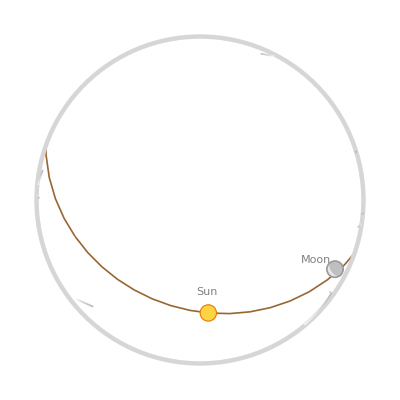
-Graphics-SENW

```mathematica
FlightsOverhead[Here,"SkyMap"]
```

### Scope

FlightsOverhead has two properties:

```mathematica
FlightsOverhead["Properties"]
```

{Flights,SkyMap}

Get an Association of properties for flights over JFK airport:

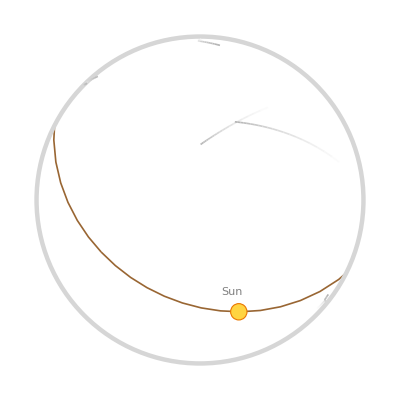
<|Flights→{PSA Airlines flight 5513,American Airlines flight 2387,Corporate Flight Management flight 154,202101080000066674,202101080000107002,CommutAir flight 4825,Southwest Airlines flight 6003},SkyMap→-Graphics-SENW|>

```mathematica
FlightsOverhead[Entity["Airport","KJFK"]]
```

## Source & Additional Information

### Contributed By

Jason Martinez

### Keywords

flights

airplane

sky map

### Categories

Geographic Data & Computation

Just For Fun

Social, Cultural & Linguistic Data

Time-Related Computation

Visualization & Graphics

### Related Symbols

AircraftData

### Related Resource Objects

SkyChart

SkyPositionChart

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

MyFunction[x,y]

## Author Notes

This will be referenced by FlightData (once that gets approved for 13.0). It should also reference that function at that point.

## Submission Notes

Additional information for the reviewer.